# Assignment 3

## Group 4

Jordan Earle - 12297127, Martin Frassek - 12236632

## Introduction

Often when biomolecular systems become complex, they cannot be reduced to elementary properties of the individual components, therefor mathematical models are often applied to the systems to understand and predict cellular functions.  Often the systems can be transformed into a system of ODE’s or PDE’s, which can be solved to assist in the understanding of the kinetics of the system.  By doing this the underlying mechanics of the system can be understood.  Two of the main methods to model molecular and gene regulatory networks are continuous (quantitative) and discrete (qualitative) modeling. 

In this experiment multiple modeling methods are used to examining chemical kinetic models.  First, qualitative chemical kinetic models are used to examine multiple signal response systems in order to determine the rates of the system and to see how the signal-response curve can be implied from the rate curves intersections.  Then the system dynamics were examined as the value of the signal was increased in a step function over time.  In the final part of this part of the experiment, 3 additional systems of ODE’s were plotted and the feedback type of each of the systems was determined from the respective equations and plots.  The dynamics of the systems were also examined and the stable points were found. 

 In the second part of the experiment, the Lac operon of Escherichia coli was examined in the frame of a signal response network.  Lactose is changed into allolactose which acts as the signal which inhibits the repressor allowing RNA polymerase to bind to the promotor and subsequently produce mRNA.  First the ODE’s which govern this reaction were examined and the terms were identified.  Next the ODE’s were solved with a set of initial conditions and the resulting mRNA concentrations with a range of lactose concentrations was examined.  Finally in this part of the experiment the the isoclines were found for the mRNA and plotted with a stream plot, and then the resulting equilibrium points were found and compared with another method ofr finding the equilibrium points.
 
In the final part of the experiment a  qualitative logical model was derived for a simple boolean network, where 3 components influenced each other.  The rules of the network were derived and a state transition table was created using the rules.  This was done manually and by implementing the rules in Mathematica to check the results.  Finally a state transition graph was created to examine what happens in the network as the system flows through different states.

## Exercise 1 - Analysing mathematical models of signal-response systems

### Background and Theory

The law of mass action, introduced by Guldberg and Wagge, states that the reaction rate is proportional to the probability of a collision occurring between the reactants. This probability is in turn proportional to the concentration of reactants to the power of the molecularity, or the number of molecules needed to enter the specific reaction.   The general form of the mass action law for a reaction with substrate S_i and a product concentration of P_j is defined as:
v = v_+- v_- = k_+Π_i S_i^m_i-k_-Π_j P_j^m_j 
where m_i and m_j denote the respective molecularity of S_i and P_j in the reaction. The rate constants which are related to the equilibrium constant can therefor be defined as:
K_eq = (k_+)/(k_-) =(∏_j P_j^m_j)/(∏_i S_i^m_i)
For example, a simple reaction of molecules A and B with k_- and k_+ kinetic/rate constants:
A  +  B (⇌_(k_-))^(k_+)  2 P
the net reaction rate is the forward rate minus the backwards rate.  From this, the rates can be written as:
v = v_++v_-= k_+A B-k_-P^2
where $v$ is the net reaction rate, $v_+$ is the forward reaction rate, and $v_-$ is the backwards reaction rate.  The system dynamics (for the concentrations of substrate) can be describes in a system of ODE’s:
dA/dt=dB/dt=- v  ,    dP/dt=2 v.
This can be generalised to systems with signal and productions, such as the signal response systems in this part of the experiment.  In this part of the experiment, signal response networks were examined using qualitative methods, creating ODE’s from the systems and examining how the signal effected the response of the system.  The systems examined can be seen in the following figure.  
-Graphics-
In the first part of the experiment, the perfect adaption network was examined.  This behaviour is typical of chemotactic systems that respond to abrupt changes in attractants or repellents and then adaprts to a constant level of signal.  An example of this kind of system is our sense of smell.  The kinetic equations of the system can be defined as:
ⅆR/ⅆt=k_1 S-k_2 X R,    
ⅆX/ⅆt=k_3 S-k_4 X
where k_1=k_2=2,k_3=k_4=1  in this experiment. In order to understand how the rates of the system respond to different signal levels, the rate curves for R were plotted as a function of R with constant values for S (S = 1,2 and 3) and the signal-response curve was also plotted and examined.  Then the concentrations of both X and R were plotted over time (0-20) as S was increased in incremental steps each 4 seconds (S = 0,1,2,3,4) and the resulting graph was analysed.  

Next, different feedforward and feedback control networks were examined.  In the figure above, b-d, 2 types of positive feedback (mutual inhibition and mutual activation) and one negative feedback examples were supplied.   In the negative feedback, the response R counteracts the effects of the stimulus signal S.  In mutual inhibition, the signal S enhances the synthesis of the response, which in turn inhibits E, in this example by phosphorylation.  In the example shown E degrades into R and therefore, E and R are mutually antagonistic.  In mutual activation the signal S enhances the synthesis of the response, which in turn enhances its own synthesis through the phosphorylating E in this example.  

In this case of mutual activation, the feedback can create a discontinuous switch, meaning the cellular response changes abruptly and irreversibly as the signal magnitude crosses a critical value S_crit, where between the values of 0 and S_crit the system is called bistable.   In the case of mutual inhibition, the feedback can create a toggle switch, where when S s decreased enough, the switch will go back to the off state.  For values of S between S_crit1 < S < S_crit2, the response of the system can be large or small.  In the case of the negative feedback, there will be a stead state concentration of the response R confined to a narrow window for a broad range of signal strengths.  

The 3 systems can be described by the following ODE’s.  In this experiment the network will be matched to the appropriate system of ODE’s.  

Negative feedback: Homeostasis

	ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01. 

In this system the signal will take values of S = 0.5, 1 and 1.5.

Positive Feedback: Mutual inhibition

	ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	
In this system the signal will take values of S = 1, 1.5 and 2. 

Positive Feedback Mutual activitation

	ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	 
In this system the signal will take values of S = 0, 8 and 16.

G in the above equations refers to the Goldbeter-Koshland function and is defined as: 
	G(u,v,J,K)=(2u K)/(v-u+v J+u K+√((v - u + v J + u K)^2- 4(v-u)u K))

From the characteristics described thus-far it may be possible to determine the type of feedback for the networks shown above.  Though in order to determine them analytically,  the rates as a function of the response for given values of the signal and the response as a function of the signal will be analysed in order to correctly classify the systems and discuss how the systems react to the signal.

### Results and Discussion

#### A1

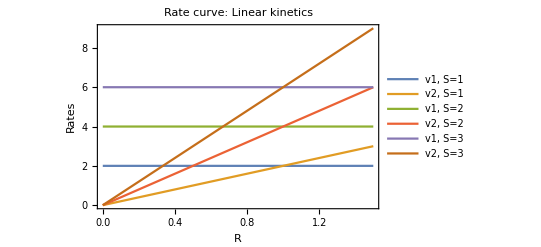

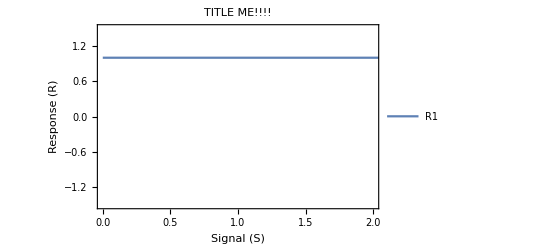

```mathematica
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};
x = k3*s/k4;
ratesa = {v1 -> k1*s, v2 -> k2*x*r};

Plot[{
v1/.ratesa/.rateconsta/.s->1,
v2/.ratesa/.rateconsta/.s->1,
v1/.ratesa/.rateconsta/.s->2,
v2/.ratesa/.rateconsta/.s->2,
v1/.ratesa/.rateconsta/.s->3,
v2/.ratesa/.rateconsta/.s->3},

{r,0,1.5},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v2, S=1", "v1, S=2", "v2, S=2", "v1, S=3", "v2, S=3"}, 
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18] ]

sol = Solve[0 == (v1-v2)/.ratesa,r][[1]][[1]];
Plot[{r/.sol/.rateconsta}, 
{s,0,5},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
PlotLegends -> {"R1", "R2", "R3"},
PlotRange->{{0,2},{-1.5,1.5}},PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

You can plot it and it would show  a constant response independent of the signal, which will be approximately 1.

#### A2

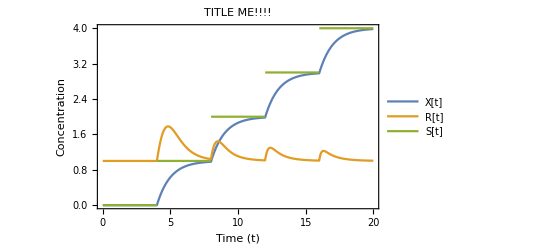

```mathematica
ClearAll["Global`*"];

s[t_] = Floor[t/4];

sol = NDSolve[Evaluate[{x'[t] == (1*s[t]) - (1*x[t]), r'[t] == (2*s[t]) - (2*x[t]*r[t]),r[0] == 1,x[0] == 0}], {x[t], r[t]}, {t, 0, 20}];
Plot[{x[t]/.sol, r[t]/.sol, s[t]}, {t,0,20},
Frame->True,FrameLabel->{"Time (t)","Concentration"},
PlotLegends -> {"X[t]","R[t]","S[t]"},
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

#### B1

Negative Feedback

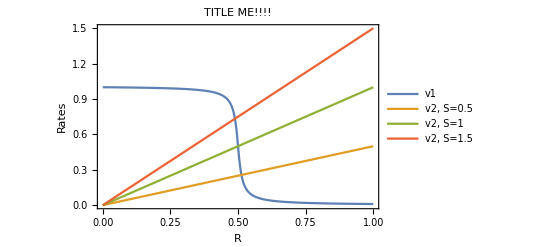

0.01/(-0.495+1.01 R+√(-0.02 (-0.5+R)+(-0.495+1.01 R)^2))-R S

```mathematica
ClearAll["Global`*"];

G[u_, v_, J_, K_] := (2*u*K)/ (v-u+v*J+u*K+√((v-u+v*J+u*K)^2 - 4(v-u)*u*K))

rateconstb = {k0 -> 1, k2 -> 1, k3 -> 0.5, k4 -> 1, J3 -> 0.01, J4 -> 0.01 };

ratesb = {v1 -> k0*G[k3,k4*R,J3,J4]/.rateconstb, v2 -> k2*S*R};

Plot[{
v1/.ratesb/.rateconstb,
v2/.ratesb/.rateconstb/.S->0.5,
v2/.ratesb/.rateconstb/.S->1,
v2/.ratesb/.rateconstb/.S->1.5,
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]

Manipulate[Plot[Evaluate[{
v1/.ratesb/.rateconstb,
R*S
}],

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18],PlotRange->{{0,1},{0,1.5}}],{S,0,10}]

(v1-v2)/.ratesb/.rateconstb

Manipulate[Plot[Evaluate[{
(v1-v2)/.ratesb/.rateconstb/.S-> O
}],

{R,0,1},Frame->True,FrameLabel->{"R","R'"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18],PlotRange->{{0,1},{0,1.5}}],{O,0,10}]
```

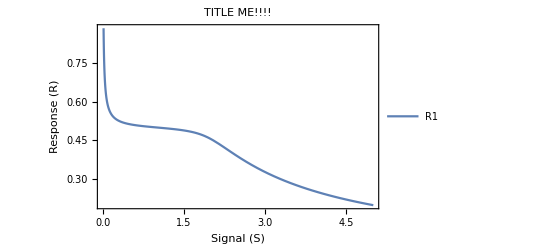

```mathematica
solb = Solve[0 == (v1-v2)/.ratesb,R][[1]];
Plot[{R/.solb[[1]]/.rateconstb}, 
{S,0,5},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
PlotLegends -> {"R1", "R2", "R3"},
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive feedback: Mutual Inhibition

S

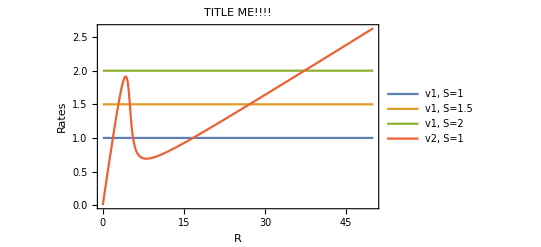

```mathematica
rateconstc = {k0 -> 0, k1 -> 1, k2 -> 0.05, k2nd -> 0.5, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesc = {v1 -> k0 + k1*S, v2 -> k2*R + k2nd*R*G[k3,k4*R,J3,J4]/.rateconstc};

v1/.ratesc/.rateconstc(*/.S->1*)

Plot[{
v1/.ratesc/.rateconstc/.S->1,
v1/.ratesc/.rateconstc/.S->1.5,
v1/.ratesc/.rateconstc/.S->2,
v2/.ratesc/.rateconstc
},

{R,0,50},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2, S=1", "v2, S=1.5", "v2, S=2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

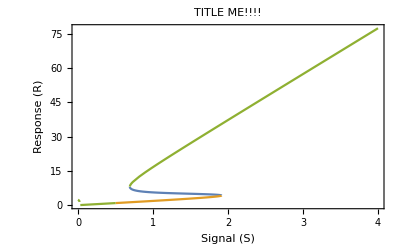

```mathematica
solc = Solve[0 == (v1-v2)/.ratesc,R];
Plot[{R/.solc[[1]]/.rateconstc,R/.solc[[2]]/.rateconstc, R/.solc[[3]]/.rateconstc}, 
{S,0,4},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive Feedback: Mutual Activation

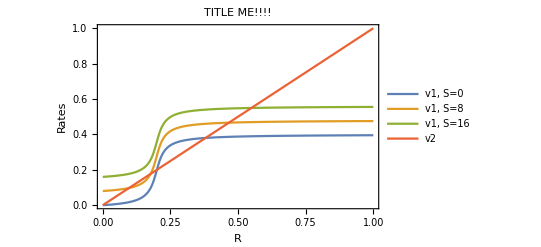

```mathematica
rateconstd = {k0 -> 0.4, k1 -> 0.01, k2 -> 1, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesd = {v1 -> k0*G[k3*R, k4, J3, J4]+k1*S, v2 -> k2*R};

Plot[{
v1/.ratesd/.rateconstd/.S->0,
v1/.ratesd/.rateconstd/.S->8,
v1/.ratesd/.rateconstd/.S->16,
v2/.ratesd/.rateconstd
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=0", "v1, S=8", "v1, S=16", "v2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

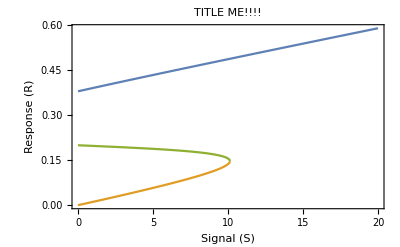

```mathematica
sold = Solve[0 == (v1-v2)/.ratesd,R];
Plot[{R/.sold[[1]]/.rateconstd,R/.sold[[2]]/.rateconstd, R/.sold[[3]]/.rateconstd}, 
{S,0,20},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

B1.b
Explain why in the homeostatic system, graphs 1, the response values are confined to a narrow window.....  They dont appear to be....  Remember to discuss stability and where the fixed points are

## Exercise 2

### Background and Theory

Hi this is text

### Results and Discussion

## Exercise 3

### Background and Theory

Hi this is text

### Results and Discussion

The bollean network was defined as:
-Graphics-
where 3 components can influence each other.  This occurs by X and Z activating Y, Y activating Z, Z inactivating X and X activating itself.  For such a simple system the  rules for the system can be defined as follows.

Rules
- X(t+1) = 0 	if 	Z(t)
- X(t+1) = 1 	if 	NOT Z(t)
- Y(t+1) = 0 	if 	NOT (X(t) AND Z(t))
- Y(t+1) = 1 	if 	X(t) AND Z(t)
- Z(t+1) = 0 	if 	NOT Y(t)
- Z(t+1) = 1 	if 	Y(t)

From this a state transition table can be constructed which takes into consideration all previous states and the resulting states at the next time step.  This can written out as it is a simple system, and can be seen in the following table.

X(t) | Y(t) | Z(t) |   | X(t+1) | Y(t+1) | Z(t+1)
0 | 0 | 0 |   | 1 | 0 | 0
0 | 0 | 1 |   | 0 | 0 | 0
0 | 1 | 0 |   | 1 | 0 | 1
0 | 1 | 1 |   | 0 | 0 | 1
1 | 0 | 0 |   | 1 | 0 | 0
1 | 0 | 1 |   | 0 | 1 | 0
1 | 1 | 0 |   | 1 | 0 | 1
1 | 1 | 1 |   | 0 | 1 | 1

In order to confirm these results, a state transition table was constructed in mathematica using the rules listed above.  This table can be seen in the following table.

```mathematica
ClearAll["Global`*"];
(*Define the rules as above. For X = 0 -> a0, X = 1-> a1, ..., etc. *)
x0[X_,Y_,Z_]:=If[Interpreter["Boolean"][Z],0]
x1[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Z]],1]
y0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][X]]&&Not[Interpreter["Boolean"][Z]],0]
y1[X_,Y_,Z_]:=If[Interpreter["Boolean"][X]&&Interpreter["Boolean"][Z],1]
z0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Y]],0]
z1[X_,Y_,Z_]:=If[Interpreter["Boolean"][Y],1]

(*Null values are generated, which have to be set to the value zero*)
x[X_, Y_, Z_]:=Apply[x0,{X, Y, Z}]/.Null->0 + Apply[x1,{X, Y, Z}]/.Null->0;
y[X_, Y_, Z_]:=Apply[y0,{X, Y, Z}]/.Null->0 + Apply[y1,{X, Y, Z}]/.Null->0;
z[X_, Y_, Z_]:=Apply[z0,{X, Y, Z}]/.Null->0+Apply[z1,{X, Y, Z}]/.Null->0;

(*Generate a list of all possible states*)
statesList = Tuples[{{0,1},{0,1},{0,1}}];

(*Apply the rules to this states list*)
listTransition = Catenate[{statesList//Transpose,{ Apply[x, statesList,1], Apply[y, statesList,1], Apply[z, statesList,1]}}]//Transpose;

(*Make a nice readable table*)
TableForm[listTransition,TableHeadings->{Automatic,{"X(t)","Y(t)","Z(t)","X(t+1)","Y(t+1)","Z(t+1)"}},TableAlignments->Center]
```

| X(t) | Y(t) | Z(t) | X(t+1) | Y(t+1) | Z(t+1)
1 | 0 | 0 | 0 | 1 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 1 | 0 | 1 | 0 | 1
4 | 0 | 1 | 1 | 0 | 0 | 1
5 | 1 | 0 | 0 | 1 | 0 | 0
6 | 1 | 0 | 1 | 0 | 1 | 0
7 | 1 | 1 | 0 | 1 | 0 | 1
8 | 1 | 1 | 1 | 0 | 1 | 1

This is the state transition graph

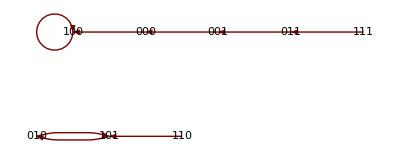

```mathematica
GraphPlot[{"000"->"100","001"->"000","010"->"101","011"-> "001",
"100"->"100","101"->"010","110"->"101","111"->"011"},DirectedEdges->True,VertexLabeling->All]
```